```mathematica
intItpr=Internal`StringToMInteger[#]&;
```

```mathematica
list=intItpr/@StringSplit[Import["/tmp/time-list","Text"],"\n"]
```

```mathematica
FromUnixTime/@list
```

```mathematica
dateList=Select[%19,Between[#,{DateObject[{2023,5,1},"Day"],Now}]&];
```

LessEqual::nordol: DateObject[{2023,5,1},Day] and DateObject[{2023,5,1,6,47,43.},Instant,Gregorian,8.] cannot be compared because they are overlapping.

LessEqual::nordol: DateObject[{2023,5,1},Day] and DateObject[{2023,5,1,6,51,53.},Instant,Gregorian,8.] cannot be compared because they are overlapping.

LessEqual::nordol: DateObject[{2023,5,1},Day] and DateObject[{2023,5,1,6,58,21.},Instant,Gregorian,8.] cannot be compared because they are overlapping.

General::stop: Further output of LessEqual::nordol will be suppressed during this calculation.

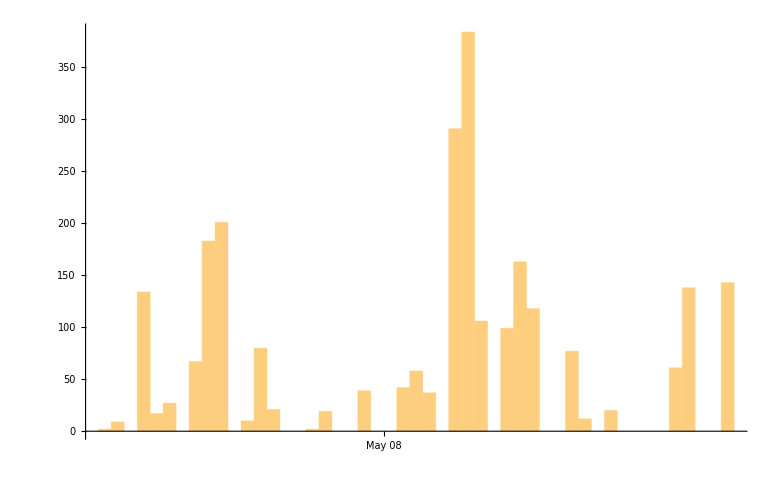

```mathematica
DateHistogram[dateList,Quantity[6, "Hours"]]
```